## Chapter 5 Problem 51: Rolf Winter’s problem

#### This notebook calculates the “exponential” decay of a state without perturbation theory

```mathematica
Remove["Global`*"]
```

Write down the solution, Equation (1) in Rolf Winter’s article

```mathematica
fFunc=HeavisideTheta[x]G Sin[q]Sin[l q];
```

```mathematica
intg=Sqrt[2/a]2n Exp[-I T q^2]q Sin[q](q Sin[q(l+1)]+f)/
((q^2-Pi^2n^2)(q^2+G q Sin[2q]+G^2Sin[q]^2));
```

Aaron’s suggestion: Change variables to integrate over a finite range

```mathematica
qu=u/(1-u);
qJac= D[qu,u];
```

Calculate the probability that the particle is inside the well as a function of time. This should resemble Figure 2 from Rolf’s paper, so use those parameters.

```mathematica
Ts={0,0.01,0.025,0.05,0.075,0.1,0.2,0.3,0.4,0.5,
1,2,4,6,8,8.25,8.5,8.75,9,9.125,9.25,9.375,9.5,9.625,9.75,9.875,
10,10.25,10.5,10.75};
```

```mathematica
vals={a->1,n->1,G->6};
```

```mathematica
t1=AbsoluteTime[];
ψ=NIntegrate[(qJac intg)/.q->qu/.vals/.f->0/.T->Ts,
{u,0,1},{l,-1,0},PrecisionGoal->4];
t2=AbsoluteTime[];
```

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::mtdfb: Numerical integration with LevinRule failed. The integration continues with Method -> MultiDimensionalRule.

General::stop: Further output of NIntegrate::mtdfb will be suppressed during this calculation.

```mathematica
(t2-t1)/60
```

4.1128593

```mathematica
ρ=Conjugate[ψ]ψ;
```

```mathematica
ρPlot=Transpose[{Ts,Re[ρ]}];
```

```mathematica
ρPlot
```

{{0,0.810615},{0.01,0.814405},{0.025,0.818401},{0.05,0.834619},{0.075,0.786283},{0.1,0.738178},{0.2,0.641932},{0.3,0.569031},{0.4,0.485395},{0.5,0.413617},{1,0.189909},{2,0.0404815},{4,0.00180554},{6,0.0000831278},{8,3.65764×10^-6},{8.25,2.36829×10^-6},{8.5,1.81344×10^-6},{8.75,1.1998×10^-6},{9,7.03745×10^-7},{9.125,6.03456×10^-7},{9.25,5.54757×10^-7},{9.375,4.98301×10^-7},{9.5,4.07987×10^-7},{9.625,3.01049×10^-7},{9.75,2.13864×10^-7},{9.875,1.68756×10^-7},{10,1.58604×10^-7},{10.25,1.41513×10^-7},{10.5,7.12582×10^-8},{10.75,4.04842×10^-8}}

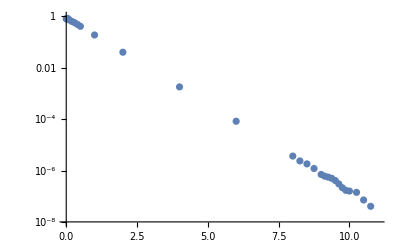

```mathematica
ListLogPlot[ρPlot,PlotRange->{{0,11},{10^(-8),1}}]
```

Fit the data to a decaying exponential to get the decay lifetime

```mathematica
fitData=Select[ρPlot,#[[1]]>1.5&&#[[1]]<8.5 &];
func=a Exp[-x/τ];
fitPars=FindFit[fitData,func,{a,τ},x]
```

{a→0.907508,τ→0.643116}

The value of τ should agree with Winter’s value 0.644 (middle, left column, page 1505)

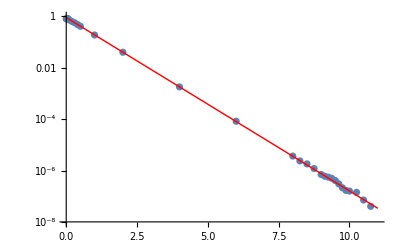

```mathematica
fitTrue=func/.fitPars;
Show[
ListLogPlot[ρPlot,PlotRange->{{0,11},{10^(-8),1}}],
LogPlot[fitTrue,{x,0,11},PlotStyle->{Thin,Red}]]
```

Use the fitted lifetime to scale the results in the small and large time region

```mathematica
ρPlotScaled=Transpose[{Ts,(Exp[Ts/τ]/.fitPars) Re[ρ]}];
```

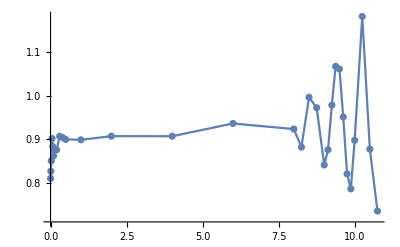

```mathematica
ListPlot[ρPlotScaled,Joined->True,Mesh->All,PlotRange->Automatic]
```

For T>8, there are oscillations with amplitude approaching 20% on top of the exponential decay.

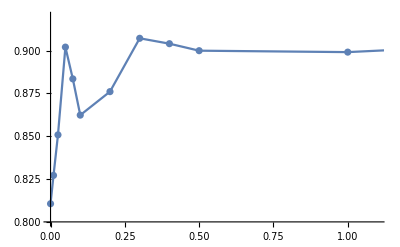

```mathematica
ListPlot[ρPlotScaled,Joined->True,Mesh->All,PlotRange->{{0,1.1},{0.8,0.92}}]
```

For T<0.5, there are also oscillations, but it is disturbing that the normalization doesn’t come out to unity at T=0. It’s worth doing some investigation of the integrand.

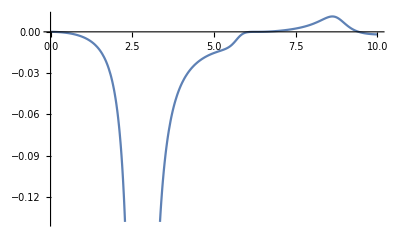

```mathematica
Plot[Integrate[intg/.vals/.f->0/.T->0,{l,-1,0}],{q,0,10}]
```